```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

PacletObject[…]

```mathematica
tMatrix[N_]:=QuantumCircuitOperator[Flatten[{If[N>=2,{Table[QuantumOperator["CZ",{i,i+1}],{i,1,N-1}],QuantumOperator["CZ",{1 ,N}]},{}],Table[QuantumOperator["H",{i}],{i,1,N}]}]];
czPart[N_]:=QuantumCircuitOperator[Flatten[{If[N>=2,{Table[QuantumOperator["CZ",{i,i+1}],{i,1,N-1}],QuantumOperator["CZ",{1 ,N}]},{}]}]];
```

```mathematica
totalMatrix[N_,n_,s_]:=QuantumCircuitOperator[Flatten[{ Table[QuantumOperator["H",{i}],{i,1,N}],Table[Flatten[{Table[QuantumOperator[{"RZ",(2 Subscript[θ, (j-1)N+i]+s[[(j-1)N+i]]Pi)},{i}],{i,1,N}] ,If[N>=2,{Table[QuantumOperator["CZ",{i,i+1}],{i,1,N-1}],QuantumOperator["CZ",{1 ,N}]},{}],Table[QuantumOperator["H",{i}],{i,1,N}]}],{j,1,n}]}]];
```

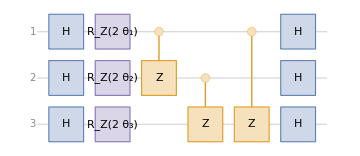

```mathematica
totalMatrix[3,1,Table[0,3*1]]["Diagram"]
```

```mathematica
toProb[unitary_]:=Table[ComplexExpand[Abs[(unitary.UnitVector[Length[unitary],1])[[i]]]^2],{i,1,Length[unitary]}]
```

## (3,1) model, verify analytic expresion in Appendix B

```mathematica
res31=toProb[totalMatrix[3,1,{0,0,0,0,0,0}]["Matrix"]];
```

compare with expression given in Appendix B of the manuscript:

```mathematica
FullSimplify[1/8(Table[1,8]+{-1,1,1,-1,1,-1,-1,1}Cos[2 Subscript[θ, 1]]Cos[2 Subscript[θ, 2]]Cos[2 Subscript[θ, 3]]+{1,1,-1,-1,-1,-1,1,1}Sin[2 Subscript[θ, 1]]Sin[2 Subscript[θ, 2]]+{1,-1,1,-1,-1,1,-1,1}Sin[2 Subscript[θ, 1]]Sin[2 Subscript[θ, 3]]+{1,-1,-1,1,1,-1,-1,1}Sin[2 Subscript[θ, 2]]Sin[2 Subscript[θ, 3]])-res31]
```

{0,0,0,0,0,0,0,0}

...and it is indeed the same.

## Further checks

Check for orthogonality:

```mathematica
basis={Table[1,8],{-1,1,1,-1,1,-1,-1,1},{1,1,-1,-1,-1,-1,1,1},{1,-1,1,-1,-1,1,-1,1},{1,-1,-1,1,1,-1,-1,1}};
```

```mathematica
Table[basis[[i]].basis[[j]],{i,1,Length[basis]-1},{j,i+1,Length[basis]}]
```

{{0,0,0,0},{0,0,0},{0,0},{0}}

Four dimensional representation of (3,1) model :

```mathematica
f31[θ1_,θ2_,θ3_]:={Cos[2θ1] Cos[2θ2] Cos[2θ3],Sin[2θ1] Sin[2θ2],Sin[2θ1] Sin[2θ3],Sin[2θ2] Sin[2θ3]};
```

Channel model already using pi/8  for all angles

```mathematica
f31MBQC[p1_,p2_,p3_]:=(1-p1)/2*(1-(1-p2)/2)*(1-(1-p3)/2)f31[Pi/4+Pi,Pi/4,Pi/4]+(1-(1-p1)/2)*(1-p2)/2*(1-(1-p3)/2)f31[Pi/4,Pi/4+Pi,Pi/4]+(1-(1-p1)/2)*(1-(1-p2)/2)*(1-p3)/2* f31[Pi/4,Pi/4,Pi/4+Pi]+((1-p1)/2)*((1-p2)/2)*(1-(1-p3)/2)*f31[Pi/4+Pi,Pi/4+Pi,Pi/4]+((1-p1)/2)*(1-(1-p2)/2)*((1-p3)/2)*f31[Pi/4+Pi,Pi/4,Pi/4+Pi]+(1-(1-p1)/2)*((1-p2)/2)*((1-p3)/2)*f31[Pi/4,Pi/4+Pi,Pi/4+Pi]+((1-p1)/2)*((1-p2)/2)*((1-p3)/2)*f31[Pi/4+Pi,Pi/4+Pi,Pi/4+Pi]+(1-(1-p1)/2)*(1-(1-p2)/2)*(1-(1-p3)/2)*f31[Pi/4,Pi/4,Pi/4];
```

```mathematica
f31MBQC[1/2,1/2,1/2]
```

{1/(16 √2),1/8,1/8,1/8}

Try to solve with Mathematica (see manuscript for analytic proof why there is no solution):

```mathematica
Solve[f31[θ1,θ2,θ3]-f31MBQC[1/2,1/2,1/2]==0,{θ1,θ2,θ3}]
```

{}

...and Mathematica also confirms that there is no solution.